### Константы

```mathematica
If[True,
A            =- 0.024 ;
B            = 1.69 ;
CC          = 0.5 ;
α            = 10^-5                 (* K^-1 *);
Subscript[T, 0]          = 300                  (* K *);
Subscript[T, avg]       = 300                  (* K *);
Young   = 1.75 * 10^11  (* Па *);
σf          = 1.1 * 10^8      (* Па *);
ϵf          = 0.000628571 ;
l            = 10                     (* Длина стержня *);
Subscript[T, f]          =22                      (* Конечный момент времени *); 
Subscript[h, t]            = 0.05               (* Шаг времени *);
a            = 50                     (* Просто константа *);
n            =  5                      (* Число узлов сетки *);
Subscript[h, x]                                          (* Шаг сетки *);
];
```

### Определение функций распределения температуры в пространстве и времени

```mathematica
F[x_] := a Sin[(π x)/l];
Subscript[T, 1][x_, t_] := Subscript[T, avg] + F[x]t Sin[t];
Subscript[T, 2][ x_, t_ ] := Subscript[T, avg] + F[x] Cos[π t^2](t+1);
TT = Subscript[T, 1];
```

Тепловые деформации

```mathematica
Subscript[ϵ, t] [x_,tt_] := α(TT[x, tt] - Subscript[T, 0]);
```

```mathematica
Subscript[u, analytical] = 
First[Flatten[
DSolve[{
D[D[u[x,t], {x, 1}]-Subscript[ϵ, t][x, t], {x, 1}]== 0,
u[0, t] == 0, 
u[l, t] == 0
},u[x,t],{x, t}]]
]⟦2⟧  // FullSimplify
```

-(t (-5+x+5 Cos[(π x)/10]) Sin[t])/(1000 π)

### Численное решение (метод конечных разностей)

Проверки для шага и количества точек (можем выставлять и то, и то)

```mathematica
If[NumberQ[n],
Subscript[h, x] = l/(n-1), 
If[NumberQ[Subscript[h, x]],n = IntegerPart[l/Subscript[h, x]]; Subscript[h, x] = l/n]
];
```

Создаем массив точек и значений функции f в них, далее решаем СЛАУ: Au = F(f(x_1), ..., f(x_n) ).

```mathematica
points = Table[i*Subscript[h, x], {i, 0, n-1}];
```

```mathematica
στ = Table[0,{i, 1, n}];                                     (* значения напряжений во временном слое τ *)
σfv = Table[σf,{i, 1, n}];                                (* значения переменных пределов прочности *)
ϵτ = Table[0,{i, 1, n}];                                            (* значения полных деформаций во временном слое τ *)
ϵe = Table[0,{i, 1, n}];                                     (* значения упругих деформаций во временном слое τ *)
ϵT = Table[0,{i, 1, n}];                                            (* значения температурных деформаций во врменном слое τ *) 
ϵcrk = Table[0,{i, 1, n}];                                        (* значения деформаций за счет трещин *) 
Tτ = Table[0,{i, 1, n}];                                            (* значения температуры во временном слое τ *) 
Subscript[balance, normal] [x_, k_]:= Young x;                             (* функция, подставляемая в условие равновесия при напряжениях, меньших предельных *) 
Subscript[balance, crack][x_, k_]:=  σfv⟦k⟧(A + B ⅇ^(-CC x/ϵf));   (* функция, подставляемая в условие равновесия при напряжениях, больших предельных *) 
balances =  Table[0,{i, 1, n}];                              (* функции равновесий на временном слое τ *) 
equations = Table[0,{i, 1, n}];                           (* линеаризованные уравнения, решениями которых являются перемещения на временном слое τ *) 
shifts = Table[0,{i, 1, n}];                                 (* сами перемещения *) 
cracking = Table[False,{i, 1, n}];                   (* нужно ли менять предел прочности*)
data = {};

For[τ = 0,τ≤Subscript[T, f],τ=τ+Subscript[h, t],
If[False, Break[]];
temp = {};
toprint = False;
For [i = 1, i≤ n+1, ++i,
Tτ⟦i⟧= TT[points⟦i⟧, τ];
ϵT⟦i⟧ = Subscript[ϵ, t][points⟦i⟧, τ];
memory =Young*( ϵτ⟦i⟧ - ϵT⟦i⟧ - ϵcrk⟦i⟧); 
balances⟦i⟧ = If[memory < σfv⟦i⟧, 
cracking⟦i⟧ = False;Subscript[balance, normal],
toprint = True;cracking⟦i⟧ = True; Subscript[balance, crack]
];
];
If[toprint,Print@{"--------", τ, "--------"};];
iterations = 0;
While[Norm[(shifts - previous)/(Norm@previous + 10^-14)] ≥ 10^-7 || iterations == 0,
++iterations; 
equations⟦1⟧ = Subscript[y, 1] == 0;
For[i = 2, i < n, ++i,
Subscript[nonElastic, i+1/2] = (ϵT⟦i+1⟧+ ϵcrk⟦i+1⟧ + ϵT⟦i⟧+ ϵcrk⟦i⟧)/2; Subscript[nonElastic, i-1/2] = (ϵT⟦i⟧+ ϵcrk⟦i⟧ + ϵT⟦i-1⟧+ ϵcrk⟦i-1⟧)/2;
Subscript[v, i+1/2]= (shifts⟦i+1⟧ - shifts⟦i⟧)/Subscript[h, x]- Subscript[nonElastic, i+1/2]; Subscript[v, i-1/2]=(shifts⟦i⟧ - shifts⟦i-1⟧)/Subscript[h, x]- Subscript[nonElastic, i-1/2];
Subscript[vnext, i+1/2] = (Subscript[y, i+1] - Subscript[y, i])/Subscript[h, x]- Subscript[nonElastic, i+1/2]; Subscript[vnext, i-1/2]= (Subscript[y, i] - Subscript[y, i-1])/Subscript[h, x]- Subscript[nonElastic, i-1/2]; 
Subscript[dσ, i+1/2]= (balances⟦i⟧[Subscript[v, i+1/2] + Subscript[h, x]/2, i] - balances⟦i⟧[Subscript[v, i+1/2], i])/(Subscript[h, x]/2); Subscript[dσ, i-1/2]=(balances⟦i⟧[ Subscript[v, i-1/2] + Subscript[h, x]/2, i] - balances⟦i⟧[ Subscript[v, i-1/2], i])/(Subscript[h, x]/2);
equations⟦i⟧ = balances⟦i⟧[Subscript[v, i+1/2], i]+Subscript[dσ, i+1/2]*(Subscript[vnext, i+1/2] - Subscript[v, i+1/2])- balances⟦i⟧[Subscript[v, i-1/2], i]-Subscript[dσ, i-1/2]*(Subscript[vnext, i-1/2] - Subscript[v, i-1/2]) == 0;
];
equations⟦n⟧ = Subscript[y, n] == 0;
If[toprint, Print[MatrixForm@equations]];
previous = shifts;
shifts = #⟦2⟧&/@First@ Solve[equations] ;
If[toprint, Print[Solve[# == 0&/@equations]]];
];
For [i = 1, i< n, ++i,
ϵτ⟦i⟧ = (shifts⟦i + 1⟧ - shifts⟦i⟧)/Subscript[h, x];
If[cracking⟦i⟧,
σfv⟦i⟧=balances⟦i⟧[ϵτ⟦i⟧ - ϵT⟦i⟧, i]; στ⟦i⟧ = σfv⟦i⟧; ϵcrk⟦i⟧ = ϵτ⟦i⟧ - ϵT⟦i⟧ - στ⟦i⟧/Young; ϵe⟦i⟧ = ϵτ⟦i⟧ - ϵT⟦i⟧ - ϵcrk⟦i⟧,
ϵe⟦i⟧ = ϵτ⟦i⟧ - ϵT⟦i⟧- ϵcrk⟦i⟧; στ⟦i⟧ = balances⟦i⟧[ϵe⟦i⟧, i]; 
];
AppendTo[temp, {τ, Tτ⟦i⟧, στ⟦i⟧, ϵτ⟦i⟧, ϵτ⟦i⟧-ϵT⟦i⟧, ϵcrk⟦i⟧}]
];
AppendTo[data, temp]
];
```

Part::partw: Part 6 of {0,5/2,5,15/2,10} does not exist.

Set::partw: Part 6 of {300,300,300,300,300} does not exist.

Part::partw: Part 6 of {0,5/2,5,15/2,10} does not exist.

Set::partw: Part 6 of {0,0,0,0,0} does not exist.

Part::partw: Part 6 of {0,0,0,0,0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::partw: Part 6 of {balance_normal,balance_normal,balance_normal,balance_normal,balance_normal} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.,0.,0.,0.,1.,0.},{0.,0.,7.×10^10,-1.4×10^11,7.×10^10,0.},{0.,7.×10^10,-1.4×10^11,7.×10^10,0.,0.},{7.×10^10,-1.4×10^11,7.×10^10,0.,0.,0.},{1.,0.,0.,0.,0.,0.}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.,0.,0.,0.,1.,0.},{0.,0.,7.×10^10,-1.4×10^11,7.×10^10,-109329.},{0.,7.×10^10,-1.4×10^11,7.×10^10,0.,0.},{7.×10^10,-1.4×10^11,7.×10^10,0.,0.,109329.},{1.,0.,0.,0.,0.,0.}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

{--------,3.55,--------}

General::munfl: Exp[-994.639] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-994.675] is too small to represent as a normalized machine number; precision may be lost.

(y_1==0
7.96839×10^6-1.75×10^11 (-0.000153468+2/5 (-y_1+y_2))+1.75×10^11 (0.000153468+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.000153468+2/5 (-y_2+y_3))+1.75×10^11 (0.000153468+2/5 (-y_3+y_4))==0
4.8003×10^6+1.04117×10^8 (0.000153468+2/5 (-y_3+y_4))-1.07957×10^8 (-0.000153468+2/5 (-y_4+y_5))==0
y_5==0)

Solve::naqs: (y_1==0)==0&&(7.96839×10^6-1.75×10^11 (-0.000153468+2/5 Plus[«2»])+1.75×10^11 (0.000153468+2/5 Plus[«2»])==0)==0&&(0.-1.75×10^11 (0.000153468+2/5 Plus[«2»])+1.75×10^11 (0.000153468+2/5 Plus[«2»])==0)==0&&(4.8003×10^6+1.04117×10^8 (0.000153468+2/5 Plus[«2»])-1.07957×10^8 (-0.000153468+2/5 Plus[«2»])==0)==0&&(y_5==0)==0 is not a quantified system of equations and inequalities.

Solve[{(y_1==0)==0,(7.96839×10^6-1.75×10^11 (-0.000153468+2/5 (-y_1+y_2))+1.75×10^11 (0.000153468+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.000153468+2/5 (-y_2+y_3))+1.75×10^11 (0.000153468+2/5 (-y_3+y_4))==0)==0,(4.8003×10^6+1.04117×10^8 (0.000153468+2/5 (-y_3+y_4))-1.07957×10^8 (-0.000153468+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

General::munfl: Exp[-1021.4] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(y_1==0
0.-1.75×10^11 (0.0110284+2/5 (-y_1+y_2))+1.75×10^11 (0.0113809+2/5 (-y_2+y_3))==0
-1.66893×10^-6-1.75×10^11 (0.0113809+2/5 (-y_2+y_3))+1.75×10^11 (0.0113809+2/5 (-y_3+y_4))==0
-9.84204×10^11+7.87363×10^11 (0.0113809+2/5 (-y_3+y_4))-0.000258834 (-0.0337903+2/5 (-y_4+y_5))==0
y_5==0)

Solve::naqs: (y_1==0)==0&&(0.-1.75×10^11 (0.0110284+2/5 Plus[«2»])+1.75×10^11 (0.0113809+2/5 Plus[«2»])==0)==0&&(-1.66893×10^-6-1.75×10^11 (0.0113809+2/5 Plus[«2»])+1.75×10^11 (0.0113809+2/5 Plus[«2»])==0)==0&&(-9.84204×10^11+7.87363×10^11 (0.0113809+2/5 Plus[«2»])-0.000258834 (-0.0337903+2/5 Plus[«2»])==0)==0&&(y_5==0)==0 is not a quantified system of equations and inequalities.

Solve[{(y_1==0)==0,(0.-1.75×10^11 (0.0110284+2/5 (-y_1+y_2))+1.75×10^11 (0.0113809+2/5 (-y_2+y_3))==0)==0,(-1.66893×10^-6-1.75×10^11 (0.0113809+2/5 (-y_2+y_3))+1.75×10^11 (0.0113809+2/5 (-y_3+y_4))==0)==0,(-9.84204×10^11+7.87363×10^11 (0.0113809+2/5 (-y_3+y_4))-0.000258834 (-0.0337903+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (-1.23897+2/5 (-y_1+y_2))+1.75×10^11 (-1.23862+2/5 (-y_2+y_3))==0
0.0000915527-1.75×10^11 (-1.23862+2/5 (-y_2+y_3))+1.75×10^11 (-1.23862+2/5 (-y_3+y_4))==0
9.80649077908024×10^1291-7.84519262326419×10^1291 (3.71621+2/5 (-y_4+y_5))==0
y_5==0)

Solve::naqs: (y_1==0)==0&&(0.-1.75×10^11 (-1.23897+2/5 Plus[«2»])+1.75×10^11 (-1.23862+2/5 Plus[«2»])==0)==0&&(0.0000915527-1.75×10^11 (-1.23862+2/5 Plus[«2»])+1.75×10^11 (-1.23862+2/5 Plus[«2»])==0)==0&&(9.80649077908024×10^1291-7.84519262326419×10^1291 (3.71621+2/5 Plus[«2»])==0)==0&&(y_5==0)==0 is not a quantified system of equations and inequalities.

General::stop: Further output of Solve::naqs will be suppressed during this calculation.

Solve[{(y_1==0)==0,(0.-1.75×10^11 (-1.23897+2/5 (-y_1+y_2))+1.75×10^11 (-1.23862+2/5 (-y_2+y_3))==0)==0,(0.0000915527-1.75×10^11 (-1.23862+2/5 (-y_2+y_3))+1.75×10^11 (-1.23862+2/5 (-y_3+y_4))==0)==0,(9.80649077908024×10^1291-7.84519262326419×10^1291 (3.71621+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

Thread::tdlen: Objects of unequal length in {-6.16552431502755+1. y_4}+{0.,-3.09743,-6.19398,-9.29052,0.} cannot be combined.

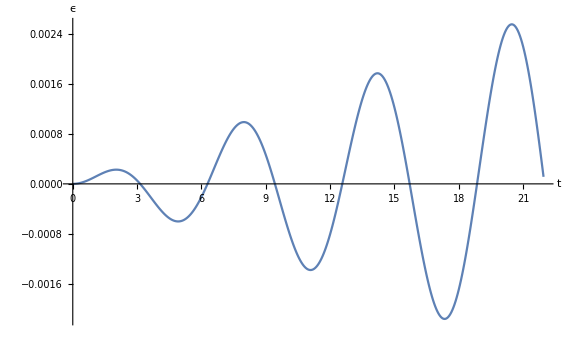

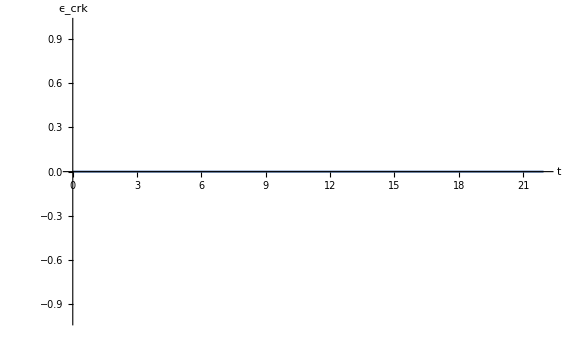

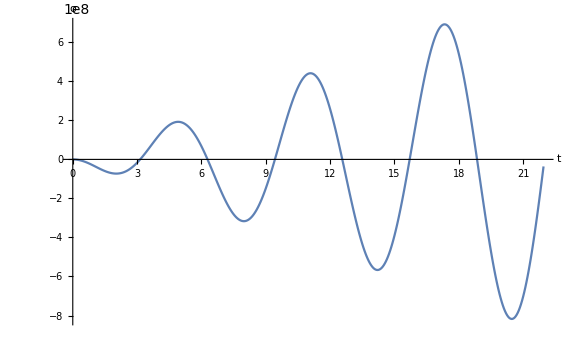

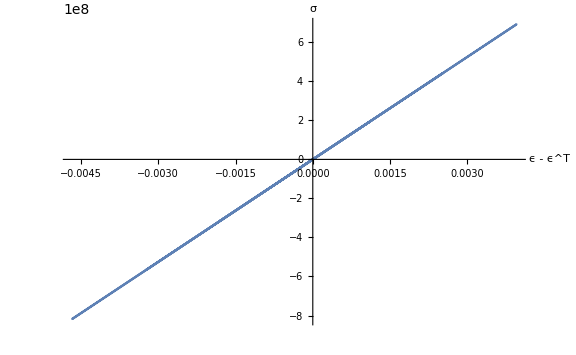

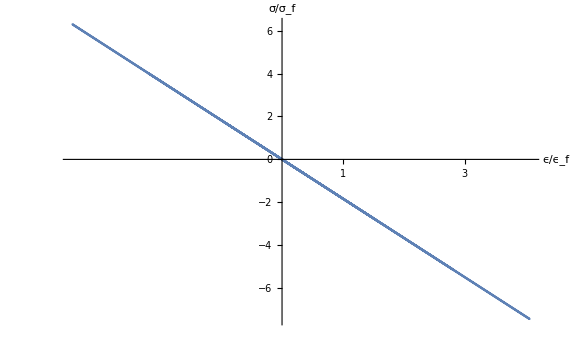

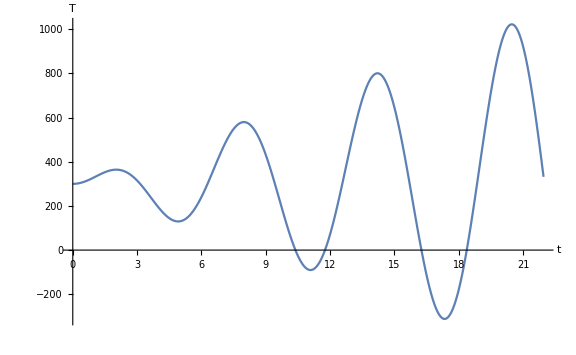

```mathematica
tϵ = ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, 4⟧}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large, AxesLabel->{"t", "ϵ"},AxesStyle->Black]
tϵcrk = ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, -1⟧}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large,  AxesLabel->{"t", "ϵ_crk"},AxesStyle->Black]
tσ = ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, 3⟧}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large,  AxesLabel->{"t", "σ"},AxesStyle->Black]
dϵσ = ListPlot[Table[{data⟦i, 2, 5⟧, data⟦i, 2, 3⟧}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True, ImageSize->Large,AxesLabel->{"ϵ - ϵ^T", "σ"},AxesStyle->Black]
normdϵσ = ListPlot[Table[{data⟦i, 2, 4⟧/ϵf, data⟦i, 2, 3⟧/σf}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large, Ticks->{Table[i,{i,1,10}], Automatic},AxesLabel->{"ϵ/ϵ_f", "σ/σ_f"},AxesStyle->Black]
tT = ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, 2⟧}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True, ImageSize->Large,AxesLabel->{"t", "T"},AxesStyle->Black ]
```

### Сохраняем графики

```mathematica
If[False, 
SetDirectory[NotebookDirectory[]];
options =StringJoin[ToString@TT~StringJoin~"/", StringJoin["h_", ToString[h] ~StringJoin~"_"], StringJoin["tau_", ToString[τ]]];
With[
{directory=FileNameJoin[{ParentDirectory@NotebookDirectory[], StringJoin["LaTeX/pic/",options ]}]},
Switch[FileType[directory],
None,CreateDirectory[directory],
Directory, Print["Overriding files in directory: "~StringJoin~directory]
];
Export[FileNameJoin[{directory, "epsilon(t).pdf"}], tϵ];
Export[FileNameJoin[{directory, "epsilon_crk(t).pdf"}], tϵcrk];
Export[FileNameJoin[{directory, "sigma(t).pdf"}], tσ];
Export[FileNameJoin[{directory, "sigma(epsilon).pdf"}], dϵσ];
Export[FileNameJoin[{directory, "norm_sigma(epsilon).pdf"}], normdϵσ];
Export[FileNameJoin[{directory, "T(t).pdf"}], tT];
]
];
```

```mathematica
Solve[{x == 1, y == 1}, {x, y}]⟦All, 1⟧
```

{x→1}